# Test the fits for the spd-Hamiltonian

```mathematica
Needs["GroupTheory`"];
```

```mathematica
dir=NotebookDirectory[]
```

/Users/tpqhe/SVN_SimPack_new/_NEW1/examples/Cu_spd/math/

## d-Hamiltonian

Read the Hamiltonian from file

```mathematica
SetDirectory[dir<>"../../../math"];
```

```mathematica
hfcc=GTReadFromFile["fcc_spd.ham"];
```

## Parameters and band structures

### parameters

```mathematica
SetDirectory[dir]
```

/Users/tpqhe/SVN_SimPack_new/_NEW1/examples/Cu_spd/math

Parameter set Papaconstantopoulos

```mathematica
cu=GTReadFromFile["parm0.parm"]
```

{{(ssσ)_1,-0.07518},{(spσ)_1,0.11571},{(ppσ)_1,0.19669},{(ppπ)_1,0.0194},{(sdσ)_1,-0.03107},{(pdσ)_1,-0.03289},{(pdπ)_1,0.01753},{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ssσ)_2,-0.00092},{(spσ)_2,0.01221},{(ppσ)_2,0.05389},{(ppπ)_2,0.00846},{(sdσ)_2,-0.00852},{(pdσ)_2,-0.00536},{(pdπ)_2,0.00321},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(ss0),0.79466},{(pp0),1.35351},{(dd0),0.37}}

Parameter set with noise [-0.02,+0.02]

```mathematica
cun=GTReadFromFile["parm1.parm"]
```

{{(ssσ)_1,-0.0767529},{(spσ)_1,0.111031},{(ppσ)_1,0.188568},{(ppπ)_1,0.000128661},{(sdσ)_1,-0.0229687},{(pdσ)_1,-0.0385961},{(pdπ)_1,0.0268663},{(ddσ)_1,-0.0282262},{(ddπ)_1,0.0333553},{(ddδ)_1,-0.018953},{(ssσ)_2,-0.00154736},{(spσ)_2,0.00986881},{(ppσ)_2,0.0634799},{(ppπ)_2,0.00557628},{(sdσ)_2,-0.0229985},{(pdσ)_2,0.0127941},{(pdπ)_2,0.0117589},{(ddσ)_2,-0.0160035},{(ddπ)_2,0.0115506},{(ddδ)_2,-0.0135301},{(ss0),0.796167},{(pp0),1.33986},{(dd0),0.366431}}

Parameter set with noise [-0.05,+0.05]

```mathematica
cun1=GTReadFromFile["parm2.parm"]
```

{{(ssσ)_1,-0.116208},{(spσ)_1,0.093824},{(ppσ)_1,0.160029},{(ppπ)_1,0.0304343},{(sdσ)_1,-0.00232342},{(pdσ)_1,0.00430486},{(pdπ)_1,-0.00457548},{(ddσ)_1,-0.0647102},{(ddπ)_1,0.00143704},{(ddδ)_1,0.00445331},{(ssσ)_2,0.0326622},{(spσ)_2,0.0206211},{(ppσ)_2,0.102987},{(ppπ)_2,0.00323903},{(sdσ)_2,-0.00576035},{(pdσ)_2,0.0126324},{(pdπ)_2,0.0421839},{(ddσ)_2,-0.0318922},{(ddπ)_2,0.00224318},{(ddδ)_2,-0.0456435},{(ss0),0.769573},{(pp0),1.30656},{(dd0),0.419182}}

### Band structure

parametrize Hamiltonian

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu];
```

calculate band structure

Maximum Abscissa = 4.48735

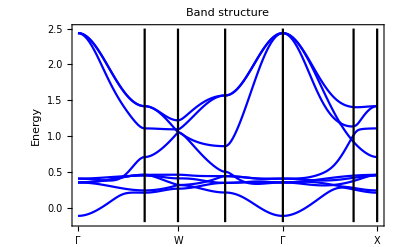

```mathematica
kp=GTBZPath["fcc"];
plt1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Blue,PlotRange->{{0,4.5},{-.2,2.5}}]
```

### comparison with test band structures

parametrize Hamiltonian with noisy parameters

Maximum Abscissa = 4.48735

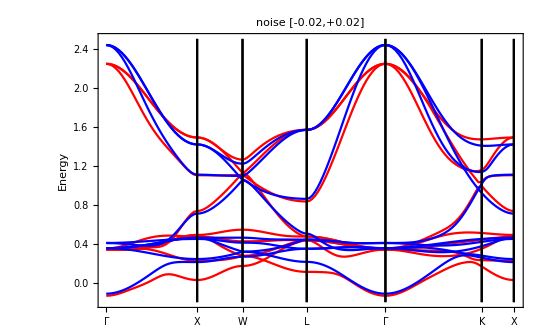

```mathematica
hfccp= hfcc /. GTTbParmToRule[cun];kp=GTBZPath["fcc"];
plt2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.5}},PlotLabel->"noise [-0.02,+0.02]"];Show[plt2,plt1]
```

Maximum Abscissa = 4.48735

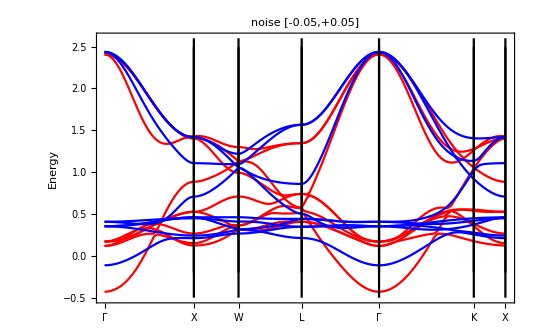

```mathematica
hfccp= hfcc /. GTTbParmToRule[cun1];kp=GTBZPath["fcc"];
plt3=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.5,2.6}},PlotLabel->"noise [-0.05,+0.05]"];Show[plt3,plt1]
```

## Least squares - Test fits with noise [-0.02,+0.02]

```mathematica
SetDirectory[dir<>"../fit/lsqr"];
```

### symmetry points

In a first step only energy values at the symmetry points are used. To reduce the number of parameters all second nearest neighbor interactions are set to zero.

Maximum Abscissa = 4.48735

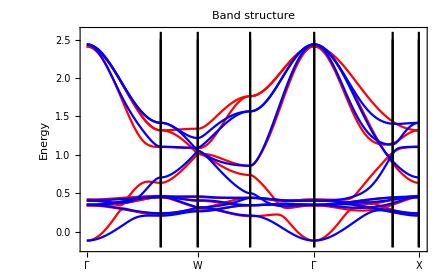

```mathematica
pfit=GTTbParmImport["cu_f1_1.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.2,2.6}}];Show[pltf1,plt1]
```

### lines X-Γ-L

All parameters are allowed to vary. The fit is already perfect.

Maximum Abscissa = 4.48735

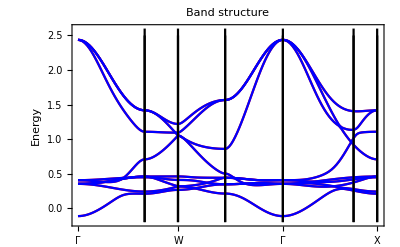

```mathematica
pfit=GTTbParmImport["cu_f1_2.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

### all lines

All parameters are allowed to vary.

```mathematica
pfit=GTTbParmImport["cu_f1_3.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf3=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf3,plt1]
```

Maximum Abscissa = 4.48735

-Graphics-

## Least squares - Test fits with noise [-0.05,+0.05]

### symmetry points

In a first step only energy values at the symmetry points are used. To reduce the number of parameters all second nearest neighbor interactions are set to zero.

Maximum Abscissa = 4.48735

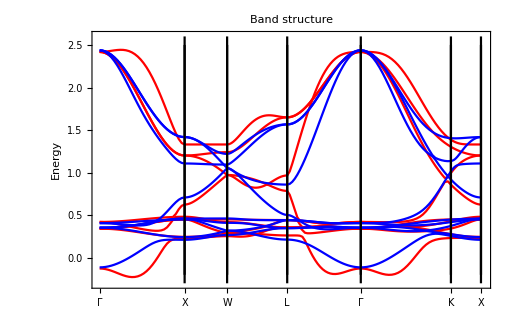

```mathematica
pfit=GTTbParmImport["cu_f2_1.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.3,2.6}}];Show[pltf1,plt1]
```

### lines X-Γ-L

All parameters are allowed to vary. Good results along X-Γ-L are achieved.

Maximum Abscissa = 4.48735

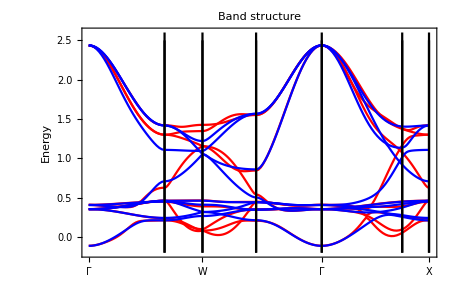

```mathematica
pfit=GTTbParmImport["cu_f2_2.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

### all lines

All parameters are allowed to vary. All lines are included. The agreement has to be improved.

Maximum Abscissa = 4.48735

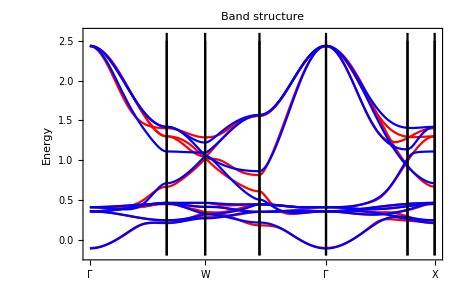

```mathematica
pfit=GTTbParmImport["cu_f2_3.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf3=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf3,plt1]
```

#### restriction to 6 bands

In a final step only the lowest 6 bands are included in the fit. The parameters reproduce the original band structure.

```mathematica
pfit=GTTbParmImport["cu_f2_4.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf4=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf4,plt1]
```

Maximum Abscissa = 4.48735

-Graphics-

## Genetic algorithm - Test fits with noise [-0.02,+0.02]

```mathematica
SetDirectory[dir<>"../fit/genetic"];
```

In this example we combine the genetic algorithm with a least square fit.

### Genetic algorithm

Maximum Abscissa = 4.48735

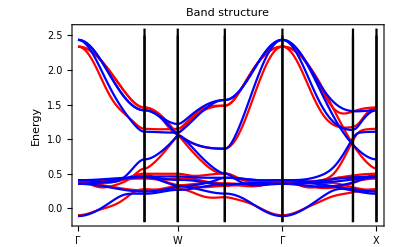

```mathematica
pfit=GTTbParmImport["cu_f1_1.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.2,2.6}}];Show[pltf1,plt1]
```

#### least squares fit

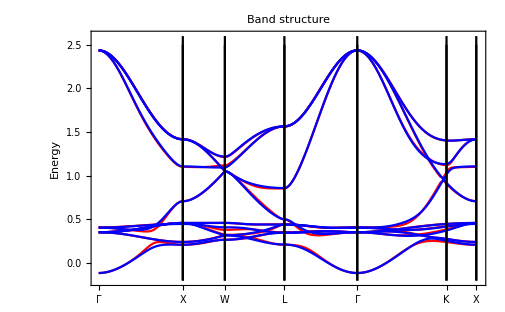

```mathematica
pfit=GTTbParmImport["cu_f1_2.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.2,2.6}}];Show[pltf1,plt1]
```

## Simplex method - Test fits with noise [-0.02,+0.02]

```mathematica
SetDirectory[dir<>"../fit/simplex1"];
```

Fixing of parameters is not used applying the simplex method

### symmetry points

Maximum Abscissa = 4.48735

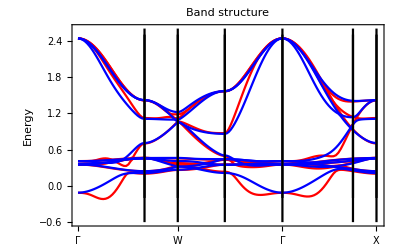

```mathematica
pfit=GTTbParmImport["cu_f1_1.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.6,2.6}}];Show[pltf1,plt1]
```

### lines X-Γ-L

Maximum Abscissa = 4.48735

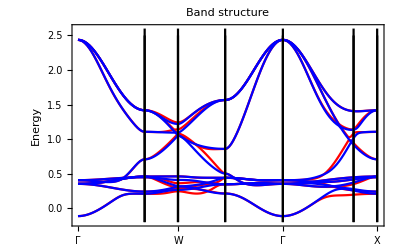

```mathematica
pfit=GTTbParmImport["cu_f1_2.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

We realize that the results along Γ-X and Γ-L are already very good.

#### inclusion of all lines

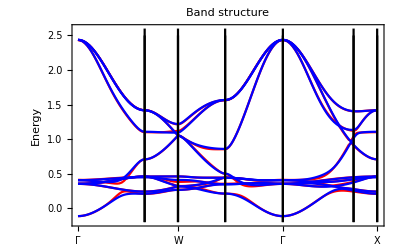

Maximum Abscissa = 4.48735

```mathematica
pfit=GTTbParmImport["cu_f1_3.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

## Simplex method - Test fits with noise [-0.05,+0.05]

```mathematica
SetDirectory[dir<>"../fit/simplex"];
```

### symmetry points

Maximum Abscissa = 4.48735

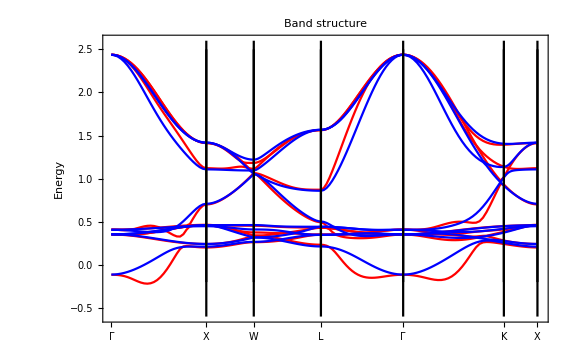

```mathematica
pfit=GTTbParmImport["cu_f2_1.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.6,2.6}}];Show[pltf1,plt1]
```

### two lines

Maximum Abscissa = 4.48735

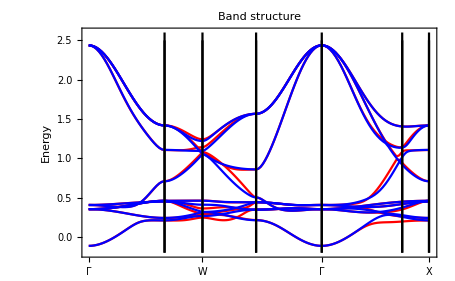

```mathematica
pfit=GTTbParmImport["cu_f2_2.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

#### all lines

Maximum Abscissa = 4.48735

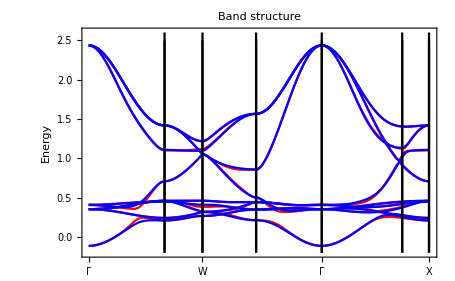

```mathematica
pfit=GTTbParmImport["cu_f2_3.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

## Simplex method - Test fits with noise [-0.05,+0.05]

```mathematica
SetDirectory[dir<>"../fit/simplex1"];
```

### symmetry points

```mathematica
pfit=GTTbParmImport["cu_f2_1.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.51},{-.6,2.6}}];Show[pltf1,plt1]
```

Maximum Abscissa = 4.48735

-Graphics-

### two lines

```mathematica
pfit=GTTbParmImport["cu_f2_2.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

Maximum Abscissa = 4.48735

-Graphics-

#### all lines

```mathematica
pfit=GTTbParmImport["cu_f2_3.parm",cu];hfccp= hfcc /. GTTbParmToRule[pfit];kp=GTBZPath["fcc"];
pltf2=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{-.2,2.6}}];Show[pltf2,plt1]
```

Maximum Abscissa = 4.48735

-Graphics-